#### Quench, over, under comparison

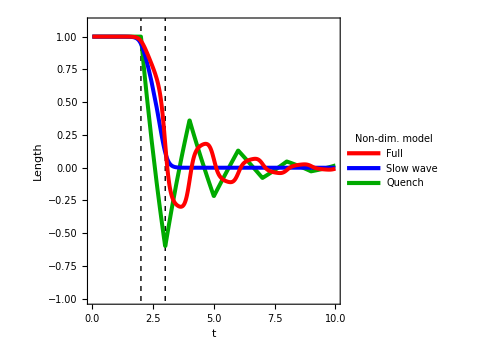

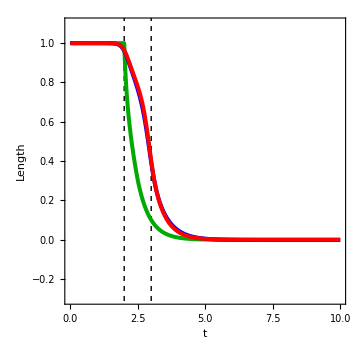

```mathematica
(* length traj curves *)
ClearAll["Global`*"];

L0=1;
c = 1;
y0[s_]:=c s;
a0=2/L0 Integrate[y0[s],{s,0,L0}];
aF[s_,n_]:=(2 c L0 (-1+Cos[n π]+n π Sin[n π]))/(n^2 π^2);
yFT[s_,NN_]:=N[a0/2+Sum[aF[s,n]Cos[(n Pi s)/L0],{n,1,NN}]]
yE[s_,t_,ηmd_,n_]:=ⅇ^(-(t ηmd)/2) Cos[n π s] (Cosh[1/2 t √(ηmd^2-4 n^2 π^2)]+(ηmd Sinh[1/2 t √(ηmd^2-4 n^2 π^2)])/(√(ηmd^2-4 n^2 π^2)));

ySol[s_,t_,ηmd_,NN_]:=N[a0/2+Sum[aF[s,n]*yE[s,t,ηmd,n],{n,1,NN}]];
lengthSol[t_,ηmd_,NN_]:=N[ySol[1,t,ηmd,NN]-ySol[0,t,ηmd,NN]];
quenchySol[s_,t_,ηmd_,NN_,o_]:=Piecewise[{{s,t<o},{ySol[s,t-o,ηmd,NN],t>=o}}]
quenchLengthSol[t_,ηmd_,NN_,o_]:=N[quenchySol[1,t,ηmd,NN,o]-quenchySol[0,t,ηmd,NN,o]];

fs  =18;
size = Medium;
SetOptions[Plot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.003],
FrameStyle->Directive[Thickness[0.003],{FontFamily->"Arial",Black,FontSize->fs}],
LabelStyle->{FontFamily->"Arial",Black,FontSize->fs}];

SetOptions[ListLogLogPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.003],
FrameStyle->Directive[Thickness[0.003],{FontFamily->"Arial",Black,FontSize->fs}],
LabelStyle->{FontFamily->"Arial",Black,FontSize->fs}];

SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.003],
FrameStyle->Directive[Thickness[0.003],{FontFamily->"Arial",Black,FontSize->fs}],
LabelStyle->{FontFamily->"Arial",Black,FontSize->fs}];


th = 0.008;
ar = 1;
plotstyle={Directive[Thickness[th],Darker@Green],Directive[Thickness[th],Blue],Directive[Thickness[th],Red]};

line1 = Line[{{2,-5},{2,5}}];
line2 = Line[{{3,-5},{3,5}}];
linestyle = {Black,Dashing[0.01],Thick};

ηm = 1;
ηd = 1;
ζ =ηd/ηm^2;
ηmd = ηd/ηm;
a = .1;
b=0;
o=2;

TMax =10;
g[s_,t_,a_,b_,o_]:=b+(1-b)/(1+Exp[(-(s-t+o))/a]);
gE[s_,t_]:=g[s,t,a,b,o];
dg[s_,t_]=D[gE[s,t],s]//Simplify;

pdeO =-(D[x[s,t],{s,2}]-dg[s,t])+ ζ D[x[s,t],t]==0;
bcO = {x[s,0]==s, (* initial profile *)
Derivative[1,0][x][0,t]==gE[0,t],
Derivative[1,0][x][1,t]==gE[1,t]};
solO=NDSolve[{pdeO,bcO},
x[s,t],
{s,0,1},
{t,0,TMax},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->300}},PrecisionGoal->5, MaxSteps->50000,AccuracyGoal->5];
xSolO[s_,t_] := Evaluate[x[s,t]/.solO];
lengthO[t_]:=xSolO[1,t]-xSolO[0,t];
velO[t_]:=Abs[Evaluate[D[lengthO[tt],tt]/.tt->t][[1]]];

pdeU = D[x[s,t],{t,2}]-(ηm)^2(D[x[s,t],{s,2}]-dg[s,t])+(ηd) D[x[s,t],t]==0;
bcU = {x[s,0]== s, (* initial profile *)
Derivative[0,1][x][s,0]==0,(* initially at rest *)
Derivative[1,0][x][0,t]==gE[0,t],
Derivative[1,0][x][1,t]==gE[1,t]};
solU=NDSolve[{pdeU,bcU},
x[s,t],
{s,0,1},
{t,0,TMax},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->300}},PrecisionGoal->5, MaxSteps->50000,AccuracyGoal->5];
xSolU[s_,t_] := Evaluate[x[s,t]/.solU];
lengthU[t_]:=xSolU[1,t]-xSolU[0,t];
velU[t_]:=Abs[Evaluate[D[lengthU[tt],tt]/.tt->t][[1]]];

pP1 = Plot[{quenchLengthSol[t*ηm,ηmd,51,(o+0)*ηm],lengthO[t],lengthU[t] },{t,0,10},
PlotRange->{-1,1.1},
AspectRatio->ar,
FrameLabel->{"t", "Length"},
PlotStyle->plotstyle,
ImageSize->size,
Prolog->{Directive[linestyle],line1,line2}];

colorList = {Red, Blue, Darker@Green};
varList = {"Full","Slow wave", "Quench"};
legend =Placed[
LineLegend[colorList, varList,
"BaseStyle"->AbsoluteThickness[3],
LabelStyle->{FontFamily->"Arial",Black,FontSize->fs},
LegendLayout->"Column",
LegendLabel->Style["Non-dim. model",Italic]
],
{Scaled[{0.95,0.95}],{0.95,0.95}}];

p1Traj = Show[Legended[Show[pP1],legend]]

ηm = 2;
ηd = 20;
ζ =ηd/ηm^2;
ηmd = ηd/ηm;
a = .1;
b=0;
o=2;

TMax =10;
g[s_,t_,a_,b_,o_]:=b+(1-b)/(1+Exp[(-(s-t+o))/a]);
gE[s_,t_]:=g[s,t,a,b,o];
dg[s_,t_]=D[gE[s,t],s]//Simplify;

pdeO =-(D[x[s,t],{s,2}]-dg[s,t])+ ζ D[x[s,t],t]==0;
bcO = {x[s,0]==s, (* initial profile *)
Derivative[1,0][x][0,t]==gE[0,t],
Derivative[1,0][x][1,t]==gE[1,t]};
solO=NDSolve[{pdeO,bcO},
x[s,t],
{s,0,1},
{t,0,TMax},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->300}},PrecisionGoal->5, MaxSteps->50000,AccuracyGoal->5];
xSolO[s_,t_] := Evaluate[x[s,t]/.solO];
lengthO[t_]:=xSolO[1,t]-xSolO[0,t];
velO[t_]:=Abs[Evaluate[D[lengthO[tt],tt]/.tt->t][[1]]];

pdeU = D[x[s,t],{t,2}]-(ηm)^2(D[x[s,t],{s,2}]-dg[s,t])+(ηd) D[x[s,t],t]==0;
bcU = {x[s,0]== s, (* initial profile *)
Derivative[0,1][x][s,0]==0,(* initially at rest *)
Derivative[1,0][x][0,t]==gE[0,t],
Derivative[1,0][x][1,t]==gE[1,t]};
solU=NDSolve[{pdeU,bcU},
x[s,t],
{s,0,1},
{t,0,TMax},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->300}},PrecisionGoal->5, MaxSteps->50000,AccuracyGoal->5];
xSolU[s_,t_] := Evaluate[x[s,t]/.solU];
lengthU[t_]:=xSolU[1,t]-xSolU[0,t];
velU[t_]:=Abs[Evaluate[D[lengthU[tt],tt]/.tt->t][[1]]];

p2Traj = Plot[{quenchLengthSol[t*ηm,ηmd,51,(o+0)*ηm],lengthO[t],lengthU[t] },{t,0,10},
PlotRange->{-0.3,1.1},
AspectRatio->ar,
FrameLabel->{"t", "Length"},
PlotStyle->plotstyle,
ImageSize->size,
Prolog->{Directive[linestyle],line1,line2}]
```

#### Calcium model

```mathematica
ClearAll["Global`*"];

D0 = 200; (* um^2/ s *)
C0 = 0.5;(* uM^*)
J0 = 1*10^7; (* uM / s *)
Γ=100; (* 1 / s *)
Cinit = J0/Γ;


L0 = 1000; (* um *)
TMax = 0.05; (* s *)

kp = 0.5; (* 1 / uM s *)
km= 0.15; (* 1 / *)
Stot = 1000; (* uM *)

SmoothStep[s_,o_,a_]:= 1/(1+Exp[(-(s-o))/a]);

pde = {D[Cd[s,t],{t,1}]-D0 D[Cd[s,t],{s,2}]+Γ Cd[s,t] +kp(Stot-Cb[s,t])Cd[s,t]-km Cb[s,t]-J0 HeavisideTheta[Cd[s,t]-C0]==0,
D[Cb[s,t],{t,1}] -kp(Stot-Cb[s,t])Cd[s,t]+km Cb[s,t]==0
};

bc = {
Cd[s,0]==Cinit*(1-SmoothStep[s,100,1] ),
Cb[s,0]==0,
Derivative[1,0][Cd][0,t]==0,
Derivative[1,0][Cd][L0,t]==0
};

sol=NDSolve[{pde,bc},
{Cd[s,t],Cb[s,t]},
{s,0,L0},
{t,0,TMax},
Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->1000}}];

CdSol[s_,t_]:=Evaluate[Cd[s,t]/.sol];
CbSol[s_,t_]:=Evaluate[Cb[s,t]/.sol];
```

NDSolve::mxsst: Using maximum number of grid points 1000 allowed by the MaxPoints or MinStepSize options for independent variable s.

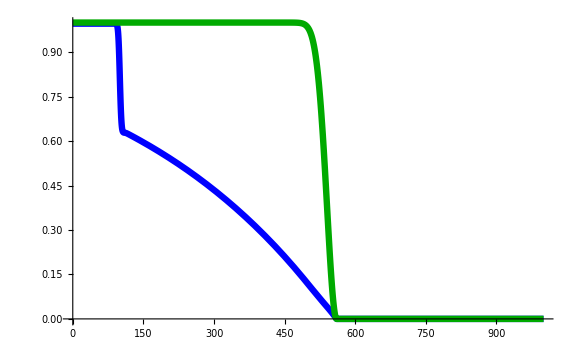

```mathematica
tp = 0.01;
plot = Show[
Plot[CdSol[s,tp][[1]]/Cinit ,{s,0,L0},ImageSize->Large, PlotStyle->Directive[Thickness[0.008],Blue]],
Plot[CbSol[s,tp][[1]]/Stot,{s,0,L0}, PlotStyle->Directive[Thickness[0.008],Darker@Green]]]
```

#### Combined trajectory fits panel - Spiro

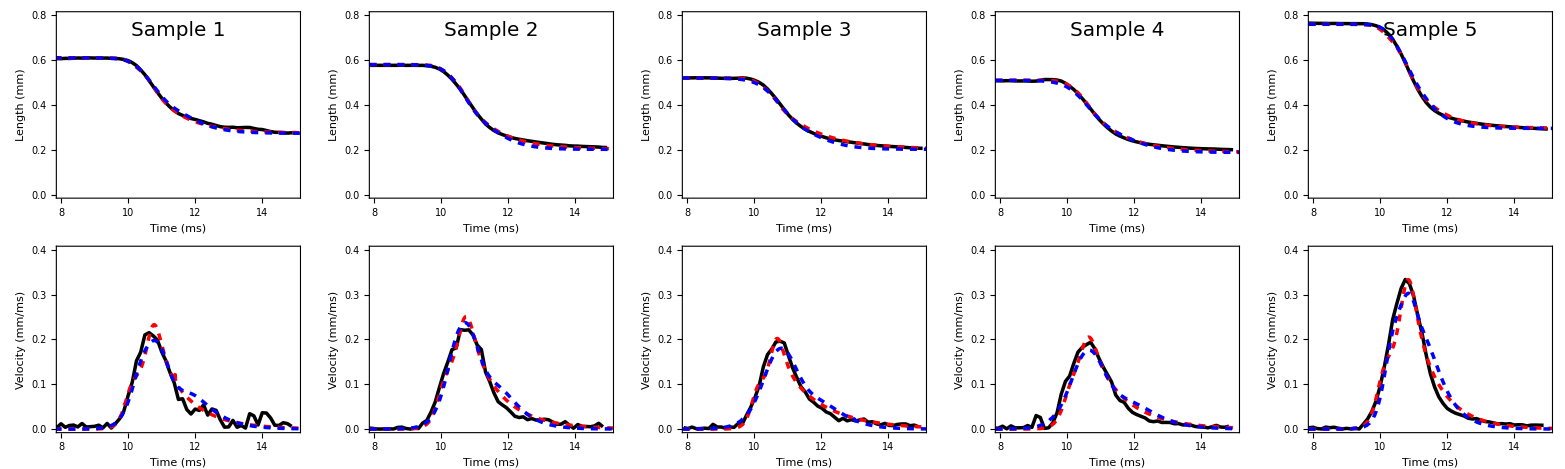

```mathematica
ClearAll["Global`*"];
pathBase = "...PathToSpiroData...";
dataOrig = Import[pathBase<>"Spiro_trajectory_data.txt","Table"];

fs = 18;
SetOptions[ListPlot,
Frame->True,
Axes->True,
FrameTicksStyle->Thickness[.003],
FrameStyle->Directive[Thickness[0.003],{FontFamily->"Arial",Black,FontSize->fs}],
LabelStyle->{FontFamily->"Arial",Black,FontSize->fs}];

SetOptions[Plot,
Frame->True,
Axes->True,
FrameTicksStyle->Thickness[.003],
FrameStyle->Directive[Thickness[0.003],{FontFamily->"Arial",Black,FontSize->fs}],
LabelStyle->{FontFamily->"Arial",Black,FontSize->fs}];


op = 0.8;
ps = 6;
th = 0.014;
thf = 0.5;
colMod = Black;
colExp = Gray;

offset = ({1.5,-0.3,1.9,-1.3,-0.8, 1}+6);
dataList = {};
dataVelList = {};
max = {345.4497412, 331.2169248, 298.7408818, 290.3577634, 491.9653088, 545};

dt = 10^-3;
TMax =30;(* ms *)
timeDomain = Range[0,TMax,dt];

bList = {0.45, 0.35, 0.39, 0.37, 0.39};
aList = {0.11, 0.12, 0.1, 0.13, 0.13};
vList = {0.8, 0.8, 0.8, 0.85, 0.9};
oList = {10,10,10,10,10};
L0List={0.61, 0.58, 0.52, 0.51, 0.76};
αList = {1,1,1,1,1};
μList={25, 28, 45,40,14};


offsetO = ({1.3,-0.55,1.55,-1.5,-0.8, 0.8}+6);
aListO = {0.14, 0.18, 0.2, 0.2, 0.15};
vListO = {0.7, 0.8, 0.7, 0.7, 0.95};
ζListO = {6,5,5,6,5}; (* = μ/α *)


facc = 5;

wind = 6;

inds = {1,2,3,4,6};

pList = {};
pVelList = {};
Do[
i = inds[[ii]];
times = Table[(i-1)*0.125,{i,1,Length[dataOrig[[;;,1]]]}];
xVals = times + offset[[i]];
yVals = MovingAverage[dataOrig[[;;,i]]*1.746 / 1000, wind];
xVals = xVals[[1;;-wind]];
data = Transpose[{xVals,yVals}];
l = data[[;;,1]];
i1=Position[l,Nearest[l,0][[1]]][[1,1]];
i2=Position[l,Nearest[l,15][[1]]][[1,1]];
plotData = data[[i1;;i2]];
velData =Abs[( plotData[[2;;-1,2]]-plotData[[1;;-2,2]])/(0.125*1)];
plotVelData = plotData[[1;;-2]];
plotVelData[[;;,2]]=velData;


b=bList[[ii]];
a=aList[[ii]];
v=vList[[ii]];
o=oList[[ii]];
L0=L0List[[ii]];
α=facc*αList[[ii]];
μ=facc*μList[[ii]];


g[s_,t_,a_,b_,o_]:=b+(1-b)/(1+Exp[(-(s-v (t-o)))/a]);
gE[s_,t_]:=g[s,t,a,b,o];
dg[s_,t_]=D[gE[s,t],s]//Simplify;
pde = D[x[s,t],{t,2}]-α(D[x[s,t],{s,2}]-dg[s,t])+μ D[x[s,t],t]==0;
bc = {x[s,0]== s, (* initial profile *)
Derivative[0,1][x][s,0]==0,(* initially at rest *)
Derivative[1,0][x][0,t]==gE[0,t],
Derivative[1,0][x][L0,t]==gE[L0,t]};
sol=NDSolve[{pde,bc},
x[s,t],
{s,0,L0},
{t,0,TMax},
Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->300}},
PrecisionGoal->5, MaxSteps->50000,AccuracyGoal->5];
xSol[s_,t_] := Evaluate[x[s,t]/.sol];
lengthM[t_]:=xSol[L0,t]-xSol[0,t];
velM[t_]:=Abs[Evaluate[D[lengthM[tt],tt]/.tt->t][[1]]];



b=bList[[ii]];
a=aListO[[ii]];
v=vListO[[ii]];
o=oList[[ii]] + (offset[[i]]-offsetO[[i]]);
L0=L0List[[ii]];
ζ = ζListO[[ii]];


gE[s_,t_]:=g[s,t,a,b,o];
dg[s_,t_]=D[gE[s,t],s]//Simplify;
g[s_,t_,a_,b_,o_]:=b+(1-b)/(1+Exp[(-(s-v (t-o)))/a]);
pde =-(D[x[s,t],{s,2}]-dg[s,t])+ ζ D[x[s,t],t]==0;
bc = {x[s,0]==s, (* initial profile *)
Derivative[1,0][x][0,t]==gE[0,t],
Derivative[1,0][x][1,t]==gE[1,t]};
solO=NDSolve[{pde,bc},
x[s,t],
{s,0,1},
{t,0,TMax},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->300}},PrecisionGoal->5, MaxSteps->50000,AccuracyGoal->5];
xSolO[s_,t_] := Evaluate[x[s,t]/.solO];
lengthMO[t_]:=xSolO[L0,t]-xSolO[0,t];
velMO[t_]:=Abs[Evaluate[D[lengthMO[tt],tt]/.tt->t][[1]]];




p=Show[
ListPlot[plotData,
PlotRange->{{8,15},{0,0.8}}, 
AspectRatio->1,
PlotStyle->Directive[Black,Thickness[thf*th],Opacity[1]],
Joined->True,
ImageSize->Medium,
FrameLabel->{"Time (ms)", "Length (mm)"},
Epilog->{Text[Style["Sample "<>ToString[ii],fs+2],Scaled[{0.5,0.9}]]}
],

Plot[lengthM[t],{t,0,TMax},
PlotStyle->Directive[Red,Dashed,Thickness[th*0.5]],
AspectRatio->1,
ImageSize->Medium
],

Plot[lengthMO[t],{t,0,TMax},
PlotStyle->Directive[Blue,Dashed,Thickness[th*0.5]],
AspectRatio->1,
ImageSize->Medium
]


];
AppendTo[pList,p];

pVel = Show[
ListPlot[plotVelData,
PlotRange->{{8,15},{0,0.4}}, 
AspectRatio->1,
PlotStyle->Directive[Black,Thickness[thf*th],Opacity[1]],
Joined->True,
ImageSize->Medium,
FrameLabel->{"Time (ms)", "Velocity (mm/ms)"}],

Plot[velM[t],{t,0,TMax},
PlotStyle->Directive[Red,Dashed,Thickness[th*0.5]],
AspectRatio->1,
PlotRange->Full,
ImageSize->Medium
],

Plot[velMO[t],{t,0,TMax},
PlotStyle->Directive[Blue,Dashed,Thickness[th*0.5]],
AspectRatio->1,
PlotRange->Full,
ImageSize->Medium
]
];
AppendTo[pVelList,pVel];

,{ii,1,5}]

totGrid=Grid[{pList,pVelList}]
```

#### Combined trajectory fits panel - Vort

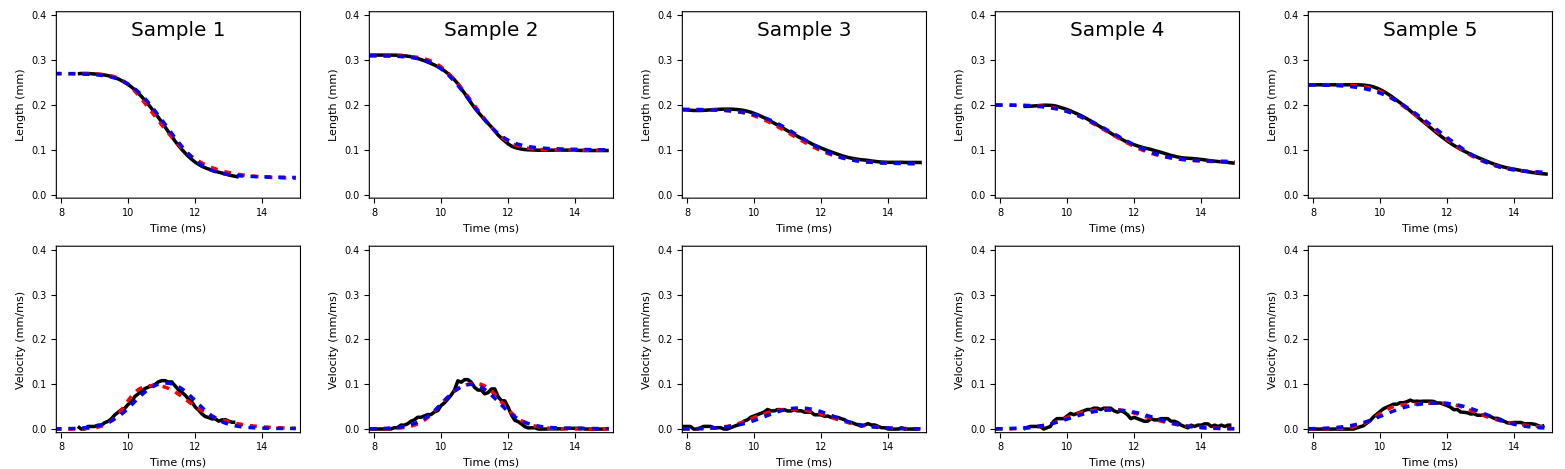

```mathematica
ClearAll["Global`*"];

fs = 18;
SetOptions[ListPlot,
Frame->True,
Axes->True,
FrameTicksStyle->Thickness[.003],
FrameStyle->Directive[Thickness[0.003],{FontFamily->"Arial",Black,FontSize->fs}],
LabelStyle->{FontFamily->"Arial",Black,FontSize->fs}];

SetOptions[Plot,
Frame->True,
Axes->True,
FrameTicksStyle->Thickness[.003],
FrameStyle->Directive[Thickness[0.003],{FontFamily->"Arial",Black,FontSize->fs}],
LabelStyle->{FontFamily->"Arial",Black,FontSize->fs}];


op = 0.8;
ps = 6;
th = 0.014;
thf = 0.5;
colMod = Black;
colExp = Gray;

pathBase = "...PathToVorticellaData.../Vorticella_trajectory_data/";
lengthFromData[dataM_]:=Module[
{data=dataM},
init = data[[1,;;]];
distList={};
Do[
p = data[[i+1,;;]];
AppendTo[distList,1.746*10^-3*N[Norm[p-init]]];
,{i,1,Length[data]-1}];
distList];

valList = {"1","2","3","4","5"};
offSet = {0.2,1.9,1.6,0,6.4}-8.7;

dt = 10^-3;
TMax =15;(* ms *)
timeDomain = Range[0,TMax,dt];

bList = {0.13, 0.32, 0.36, 0.36,0.18};
aList = {0.08, 0.08, 0.05, 0.05, 0.04};
vList = {0.3, 0.25, 0.13, 0.13,0.13};
oList = {10,10.0,10.0,10.0,10.0};
L0List={0.27,0.31,0.19,0.2,0.245};
αList = {1,1,1,1,1};
μList={30,10,45,45,40};

offSetO = {0.4,2.0,2.0,0.1,6.5}-8.7;
aListO = {0.06, 0.08, 0.05, 0.04, 0.04};
vListO = {0.15, 0.2, 0.1, 0.08,0.08};
ζListO = {2,1,1,3,4};

wind = 6;


pList = {};
pVelList = {};
Do[
data = Import[pathBase<>"water10k_"<>valList[[ii]]<>".txt","Table"];
xVals =0.1*Range[0,Length[data]-2] - offSet[[ii]];
yVals = MovingAverage[lengthFromData[data],wind];
xVals = xVals[[1;;-wind]];
data = Transpose[{xVals,yVals}];
l = data[[;;,1]];
i1=Position[l,Nearest[l,0][[1]]][[1,1]];
i2=Position[l,Nearest[l,15][[1]]][[1,1]];
plotData = data[[i1;;i2]];
velData =Abs[( plotData[[2;;-1,2]]-plotData[[1;;-2,2]])/(0.1*1)];
plotVelData = plotData[[1;;-2]];
plotVelData[[;;,2]]=velData;


b=bList[[ii]];
a=aList[[ii]];
v=vList[[ii]];
o=oList[[ii]];
L0=L0List[[ii]];
α=αList[[ii]];
μ=μList[[ii]];


g[s_,t_,a_,b_,o_]:=b+(1-b)/(1+Exp[(-(s-v (t-o)))/a]);
gE[s_,t_]:=g[s,t,a,b,o];
dg[s_,t_]=D[gE[s,t],s]//Simplify;
pde = D[x[s,t],{t,2}]-α(D[x[s,t],{s,2}]-dg[s,t])+μ D[x[s,t],t]==0;
bc = {x[s,0]== s, (* initial profile *)
Derivative[0,1][x][s,0]==0,(* initially at rest *)
Derivative[1,0][x][0,t]==gE[0,t],
x[L0,t]==L0};
sol=NDSolve[{pde,bc},
x[s,t],
{s,0,L0},
{t,0,TMax},
Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->1000}},
"MaxSteps"->10000,
AccuracyGoal->8];
xSol[s_,t_] := Evaluate[x[s,t]/.sol];
lengthM[t_]:=xSol[L0,t]-xSol[0,t];
velM[t_]:=Abs[Evaluate[D[lengthM[tt],tt]/.tt->t][[1]]];


b=bList[[ii]];
a=aListO[[ii]];
v=vListO[[ii]];
o=oList[[ii]] - (offSet[[ii]]-offSetO[[ii]]);
L0=L0List[[ii]];
ζ = ζListO[[ii]];


gE[s_,t_]:=g[s,t,a,b,o];
dg[s_,t_]=D[gE[s,t],s]//Simplify;
g[s_,t_,a_,b_,o_]:=b+(1-b)/(1+Exp[(-(s-v (t-o)))/a]);
pde =-(D[x[s,t],{s,2}]-dg[s,t])+ ζ D[x[s,t],t]==0;
bc = {x[s,0]==s, (* initial profile *)
Derivative[1,0][x][0,t]==gE[0,t],
Derivative[1,0][x][1,t]==gE[1,t]};
solO=NDSolve[{pde,bc},
x[s,t],
{s,0,1},
{t,0,TMax},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->2000,"MinPoints"->1000}},PrecisionGoal->8, MaxSteps->50000,AccuracyGoal->8];
xSolO[s_,t_] := Evaluate[x[s,t]/.solO];
lengthMO[t_]:=xSolO[L0,t]-xSolO[0,t];
velMO[t_]:=Abs[Evaluate[D[lengthMO[tt],tt]/.tt->t][[1]]];


p=Show[
ListPlot[plotData,
PlotRange->{{8,15},{0,0.4}}, 
AspectRatio->1,
PlotStyle->Directive[Black,Thickness[thf*th],Opacity[1]],
Joined->True,
ImageSize->Medium,
FrameLabel->{"Time (ms)", "Length (mm)"},
Epilog->{Text[Style["Sample "<>ToString[ii],fs+2],Scaled[{0.5,0.9}]]}
],

Plot[lengthM[t],{t,0,TMax},
PlotStyle->Directive[Red,Dashed,Thickness[th*0.5]],
AspectRatio->1,
ImageSize->Medium
],

Plot[lengthMO[t],{t,0,TMax},
PlotStyle->Directive[Blue,Dashed,Thickness[th*0.5]],
AspectRatio->1,
ImageSize->Medium
]


];
AppendTo[pList,p];

pVel = Show[
ListPlot[plotVelData,
PlotRange->{{8,15},{0,0.4}}, 
AspectRatio->1,
PlotStyle->Directive[Black,Thickness[thf*th],Opacity[1]],
Joined->True,
ImageSize->Medium,
FrameLabel->{"Time (ms)", "Velocity (mm/ms)"}],

Plot[velM[t],{t,0,TMax},
PlotStyle->Directive[Red,Dashed,Thickness[th*0.5]],
AspectRatio->1,
PlotRange->Full,
ImageSize->Medium
],

Plot[velMO[t],{t,0,TMax},
PlotStyle->Directive[Blue,Dashed,Thickness[th*0.5]],
AspectRatio->1,
PlotRange->Full,
ImageSize->Medium
]
];
AppendTo[pVelList,pVel];

,{ii,1,5}]


totGrid=Grid[{pList,pVelList}]
```

#### Combined scaling

{1.,5.05309,13.3565,25.5337,67.4914}

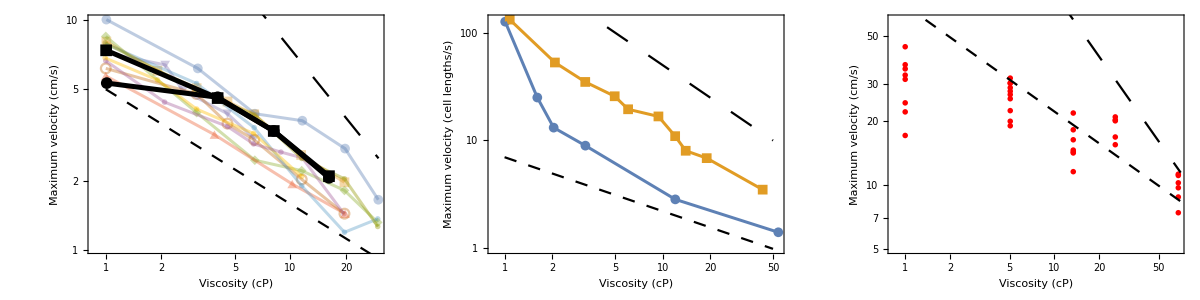

```mathematica
ClearAll["Global`*"];
pathBase = "...PathToUpadhyayaScaling...";
dataList = List[];

Do[
data = Import[pathBase<>"/UpadhyayaScaling"<>ToString[i]<>".csv"];

AppendTo[dataList, data];
,{i,1,10}]

fs = 18;
SetOptions[ListLogLogPlot,
Frame->True,
Axes->True,
FrameTicksStyle->Thickness[.003],
FrameStyle->Directive[Thickness[0.003],{FontFamily->"Arial",Black,FontSize->fs}],
LabelStyle->{FontFamily->"Arial",Black,FontSize->fs}];

op = 0.4;

pA=Show[
ListLogLogPlot[dataList,
ImageSize->Medium, 
AspectRatio->1,
FrameLabel->{"Viscosity (cP)", "Maximum velocity (cm/s)"},
PlotMarkers->{Automatic,AbsolutePointSize[10]},
PlotStyle->Directive[Opacity[op]]],

ListLogLogPlot[dataList,
Joined->True,
PlotStyle->Directive[Thickness[0.006],Opacity[op]]],

LogLogPlot[{5*x^(-1/2),75*x^-1},{x,1,30},PlotStyle->{Directive[Black,Dashing[0.025]],Directive[Black,Dashing[0.05]]}]
];

pathBase = "...PathToMisraScaling...";
dataListM = List[];

Do[

data = Import[pathBase<>"MisraScaling"<>ToString[i]<>".csv"];
AppendTo[dataListM, data];
,{i,1,2}]

pM=Show[
ListLogLogPlot[dataListM,
ImageSize->Medium, 
AspectRatio->1,
FrameLabel->{"Viscosity (cP)", "Maximum velocity (cm/s)"},
PlotMarkers->{Automatic,AbsolutePointSize[12]},
PlotStyle->Directive[Black,Opacity[1]]],

ListLogLogPlot[dataListM,
Joined->True,
PlotStyle->Directive[Black,Thickness[0.01]]]
];

pV=Show[pA,pM];





pathBase = "...PathToHawkesScaling...";
dataList = List[];
Do[

data = Import[pathBase<>"HawkesScaling"<>ToString[i]<>".csv"];
data[[;;,1]] =100* data[[;;,1]] ;

AppendTo[dataList, data];
,{i,1,2}]


pS=Show[
ListLogLogPlot[dataList,
ImageSize->Medium, 
AspectRatio->1,
FrameLabel->{"Viscosity (cP)", "Maximum velocity (cell lengths/s)"},
PlotMarkers->{Automatic,AbsolutePointSize[10]},
PlotStyle->Directive[Opacity[1]]],

ListLogLogPlot[dataList,
Joined->True,
PlotStyle->Directive[Thickness[0.006]]],

LogLogPlot[{7*x^(-1/2),500*x^-1},{x,1,50},PlotStyle->{Directive[Black,Dashing[0.025]],Directive[Black,Dashing[0.05]]}]
];



water={35.17657700471999,36.79469671716,44.7020954262,32.87265003792002,31.416608257919975,22.069166471640006,17.091195318359993,24.339373603919995};
f10 ={22.366787536440004,27.606614376240014,30.065037200640006,30.204076348799997,31.82202044856,28.671800681879994,26.61556780511999,19.937882099160017,25.448267352960006,18.981663094800012};
f16 ={21.797300792519998,16.313004864360007,14.308068070800012,14.14386316116001,18.17663473511999,11.546427238920007,14.587365878280009};
f20 = {20.896339545360007,20.239216137720007,16.811124626519998,15.46621585128001,20.033869426919996};
f26 ={8.774235119519997,11.236005829079993,10.231021289160008,11.08036124315999,9.698739290999999,7.400570911560004};



CC = {0, 10, 16, 20, 26}/1;
η=Exp[CC * 0.162]
fac = 1;
means = fac*Abs[{Mean[water],Mean[f10],Mean[f16],Mean[f20],Mean[f26]}] ;
stds =  fac*Abs[{StandardDeviation[water],StandardDeviation[f10],StandardDeviation[f16],StandardDeviation[f20],StandardDeviation[f26]}] ;
meds = fac*Abs[{Median[water],Median[f10],Median[f16],Median[f20],Median[f26]}];
mads =  fac*Abs[{MedianDeviation[water],MedianDeviation[f10],MedianDeviation[f16],MedianDeviation[f20],MedianDeviation[f26]}] ;

xW = Table[η[[1]],{i,1,Length[water]}];
dw = Transpose[{xW,water}];
x10 = Table[η[[2]],{i,1,Length[f10]}];
d10 = Transpose[{x10,f10}];
x16 = Table[η[[3]],{i,1,Length[f16]}];
d16 = Transpose[{x16,f16}];
x20 = Table[η[[4]],{i,1,Length[f20]}];
d20 = Transpose[{x20,f20}];
x26 = Table[η[[5]],{i,1,Length[f26]}];
d26 = Transpose[{x26,f26}];
data = Join[dw,d10,d16,d20,d26];



marker=Graphics[{EdgeForm[{Thickness[0.1],Green}],Circle[Offset[{2,2},{10,0}],0.1]},ImageSize->10];

pOurs = Show[
ListLogLogPlot[data, PlotRange->{5,60},
AspectRatio ->1, PlotStyle->{AbsolutePointSize[7],Directive[Red]},
ImageSize->Medium,
PlotMarkers->{Graphics@{Red,Disk[]},0.025},
(*Method->{"OptimizePlotMarkers"->False},*)
BaseStyle->Opacity[.999],
FrameLabel->{"Viscosity (cP)","Maximum velocity (cm/s)"}],

LogLogPlot[{70*x^(-1/2),800*x^-1},{x,1,70}, PlotStyle->{Directive[Black,Dashing[0.025]],Directive[Black,Dashing[0.05]]}]
];



pTot = Grid[{{pV,pS,pOurs}}]
```